# The Madelung energy of an ionic crystal

Angel Salazar
School of Physical Sciences and Nanotechnology

Consider a 2D lattice from a rocksalt crystal (called bipartite lattice). Obtain the madelung energy (electrostatic energy) and show how the calculation is sensitive to the way in which the infinite sum is truncated (squares or circles)

```mathematica
sqSum[n_]:=Sum[If[i==j==0,0,N[(-1)^(i+j)/(√(i^2+j^2))]],{i,-n,n},{j,-n,n}]
```

```mathematica
crSum[n_]:=Sum[If[√(i^2+j^2)>n ∨ i==j==0,0,N[(-1)^(i+j)/(√(i^2+j^2))]],{i,-n,n},{j,-n,n}](*v is esc+or+esc*)
```

Let’s understand what is doing sqSum[n]

```mathematica
sqSum[1]
```

-1.17157

```mathematica
Table[If[i==j==0,0,f[i,j]],{i,-1,1},{j,-1,1}]//Flatten
```

{f[-1,-1],f[-1,0],f[-1,1],f[0,-1],0,f[0,1],f[1,-1],f[1,0],f[1,1]}

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->-1}
```

0.707107

```mathematica
+N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->0}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->-1,j->1}
```

0.707107

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->0,j->-1}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->0,j->1}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->-1}
```

0.707107

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->0}
```

-1.

```mathematica
N[(-1)^(i+j)/(√(i^2+j^2))]/.{i->1,j->1}
```

0.707107

```mathematica
4*0.7071067811865475+4*-1
```

-1.17157

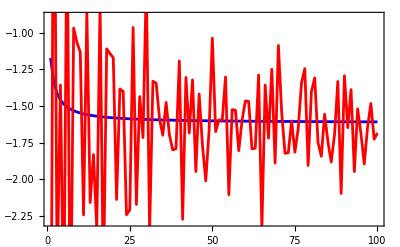

```mathematica
DiscretePlot[
{sqSum[n],crSum[n]},{n,1,100},
Filling->None,
Frame->True,
Joined->True,
PlotStyle->{Blue,Red}


]
```

```mathematica
data=-Graphics-
```

-Graphics-

```mathematica
line =data[[1,4,4,1,1]];
```

```mathematica
line[[All,2]]
```

{-1.17157,-1.33507,-1.41457,-1.45889,-1.48724,-1.50692,-1.52137,-1.53243,-1.54116,-1.54824,-1.55408,-1.559,-1.56318,-1.56679,-1.56993,-1.5727,-1.57514,-1.57733,-1.57929,-1.58105,-1.58266,-1.58412,-1.58546,-1.58668,-1.58782,-1.58886,-1.58983,-1.59073,-1.59157,-1.59236,-1.5931,-1.59379,-1.59444,-1.59505,-1.59563,-1.59617,-1.59669,-1.59718,-1.59764,-1.59808,-1.5985,-1.59891,-1.59929,-1.59965,-1.6,-1.60034,-1.60066,-1.60096,-1.60126,-1.60154,-1.60181,-1.60207,-1.60233,-1.60257,-1.6028,-1.60303,-1.60325,-1.60346,-1.60366,-1.60386,-1.60405,-1.60423,-1.60441,-1.60458,-1.60475,-1.60491,-1.60507,-1.60522,-1.60537,-1.60551,-1.60565,-1.60579,-1.60592,-1.60605,-1.60618,-1.6063,-1.60642,-1.60653,-1.60665,-1.60676,-1.60687,-1.60697,-1.60707,-1.60717,-1.60727,-1.60737,-1.60746,-1.60755,-1.60764,-1.60773,-1.60781,-1.6079,-1.60798,-1.60806,-1.60814,-1.60822,-1.60829,-1.60836,-1.60844,-1.60851}

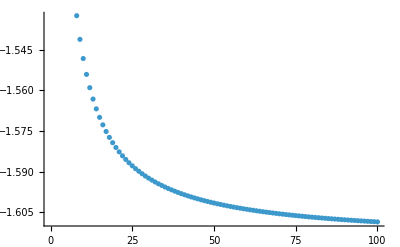

```mathematica
line//ListPlot
```

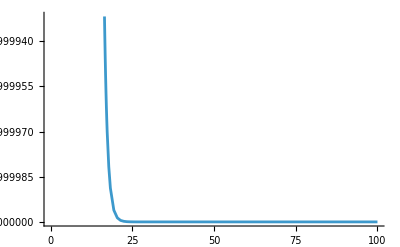

```mathematica
Plot[Exp[-1 x]-1.6,{x,0,100}]
```

### model 1

```mathematica
model1 = c[1]+c[2] Exp[-c[3] x]+c[4] x^(-c[5]);
```

```mathematica
nlm1=NonlinearModelFit[line,model1,Table[c[n],{n,5}],x]
```

FittedModel[…]

```mathematica
nlm1[x]
```

-1.61699-0.797536 ⅇ^(-1.87376 x)+0.567911/x^0.919467

```mathematica
nlm1["RSquared"]//NumberForm[#,16]&
```

0.999999970625266

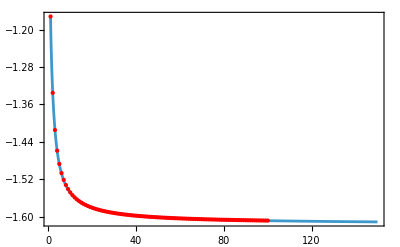

```mathematica
Plot[nlm1[x],{x,1,150},
Frame->True,
Epilog->{Red,Point[line]},
PlotRange->All
]
```

```mathematica
Limit[nlm1[x],x->∞]
```

-1.61699